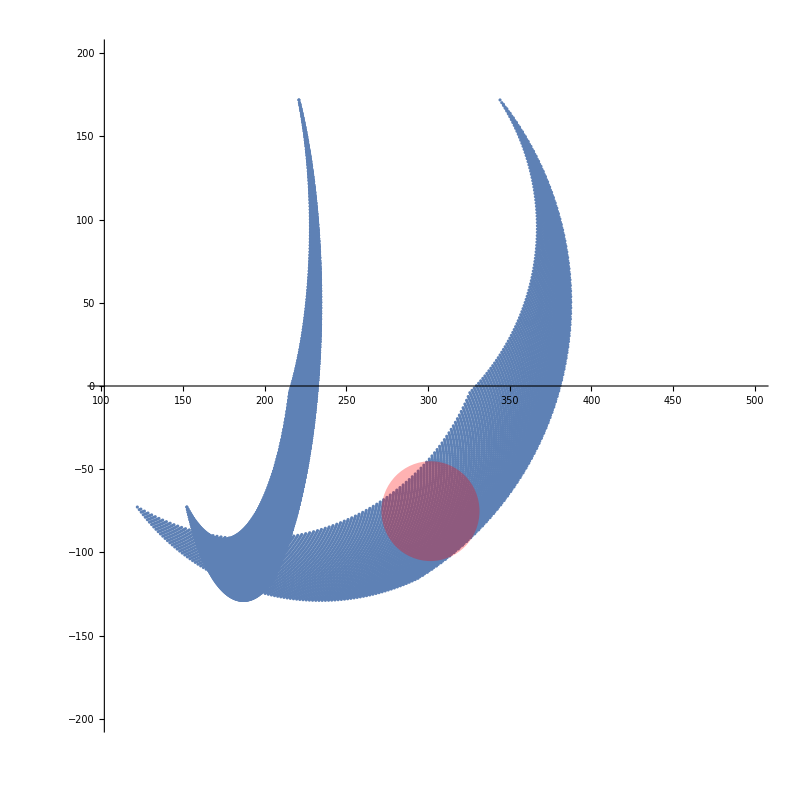

{301.198,0.,-74.9346}

```mathematica
TIPTOWRIST=140;
WRISTTOKNEE=56;
KNEETOSHOULDER=28;
CENTERTOSHOULDER=166;
KNEETOBOTTOM=50;
KNEEMINANGLE=35.0*Pi/180;
KNEEMAXANGLE=135.0*Pi/180;
WRISTMINANGLE=20.0*Pi/180;
WRISTMAXANGLE=100.0*Pi/180;
SHOULDERMINANGLE=-90.0*Pi/180;
SHOULDERMAXANGLE=90.0*Pi/180;

Dist[K_,W_]:=KNEETOSHOULDER+WRISTTOKNEE*Sin[K]+TIPTOWRIST*Sin[K+W];
Sh[L_]:={CENTERTOSHOULDER*Cos[L*Pi/3],CENTERTOSHOULDER*Sin[L*Pi/3]};
AngToPos[K_, W_, S_,L_]:={Sh[L][[1]]+Dist[K,W]*Cos[S+L*Pi/3],Sh[L][[2]]+Dist[K,W]*Sin[S+L*Pi/3],KNEETOBOTTOM+WRISTTOKNEE*Cos[K]+TIPTOWRIST*Cos[K+W]};
AngToPosNormalized[K_, W_, S_,L_]:=AngToPos[K*(KNEEMAXANGLE-KNEEMINANGLE)+KNEEMINANGLE,W*(WRISTMAXANGLE-WRISTMINANGLE)+WRISTMINANGLE,S*(SHOULDERMAXANGLE-SHOULDERMINANGLE)+SHOULDERMINANGLE,L];
angs:=Flatten[Outer[{#1,#2,#3}&,Range[0.01,0.99,0.01],Range[0.01,0.99,0.01],Range[0.1,0.9,0.4]],2];
h=-75;
pts[L_]=Map[{#[[1]],#[[3]]}&,Select[Map[AngToPosNormalized[#[[1]],#[[2]],#[[3]],L]&,angs],Abs[#[[3]]-h]<5000&]];
(*cb[k_]:=AngToPosNormalized[0.54,0.625,0.5,k]+{0, 0};*)
cb[k_]:=AngToPosNormalized[0.496,0.673,0.5,k]+{0,0,0};
Show[ListPlot[Map[pts[#]&,Range[0,0]],ImageSize->{800,800},PlotRange->{{100,500},{-200,200}},AspectRatio->1],Graphics[{Red,Opacity[0.3],Ball[{cb[0][[1]],cb[0][[3]]},30]}]]
(*points:=ListPointPlot3D[Map[pts[#]&,Range[0,0]],PlotRange->Full,RotationAction->"Clip"];
origins=Map[Graphics3D[{Red,Ball[{CENTERTOSHOULDER*Cos[#*Pi/3],CENTERTOSHOULDER*Sin[#*Pi/3],KNEETOBOTTOM},5]}]&,Range[0,0]];
spans:=Map[{Graphics3D[{Red,Ball[cb[#],30]}]}&,Range[0,0]];
Show[Join[spans,{points},origins]]*)
cb[0]
```

```mathematica
f
```

```mathematica
x=301.088;
y=0;
z=-75;
u=x-Sh[0][[1]];
v=y-Sh[0][[2]];
P=Sqrt[u*u+v*v] - KNEETOSHOULDER;
Q=z-KNEETOBOTTOM;
SS=P*P+Q*Q;
W=Pi-ArcCos[(TIPTOWRIST*TIPTOWRIST+WRISTTOKNEE*WRISTTOKNEE-SS)/TIPTOWRIST/WRISTTOKNEE/2];
W=(W-WRISTMINANGLE)/(WRISTMAXANGLE-WRISTMINANGLE)//N
a=ArcCos[(WRISTTOKNEE*WRISTTOKNEE + SS  - TIPTOWRIST*TIPTOWRIST)/WRISTTOKNEE/Sqrt[SS]/2];
b=ArcTan[Abs[Q],Abs[P]];
(Pi-a-b-KNEEMINANGLE)/(KNEEMAXANGLE-KNEEMINANGLE)
```

0.673344

0.496218